```mathematica
F[x_,y_]:=1/((x^2+y^2)^Δ)
G[x_,y_]:=1/(2π σ^2)Exp[-1/2(x^2+y^2)/σ^2]
```

```mathematica
kF=FourierTransform[F[x,y],{x,y},{kx,ky}]
kG=FourierTransform[G[x,y],{x,y},{kx,ky}]//FullSimplify[#,Element[σ,Reals]]&
```

(2^(1-2 Δ) (kx^2+ky^2)^(1/2 (-2+2 Δ)) Gamma[1-Δ])/Gamma[Δ]

(ⅇ^(-1/2 (kx^2+ky^2) σ^2))/(2 π)

```mathematica
kF kG kG //FullSimplify
```

(2^(-1-2 Δ) ⅇ^(-((kx^2+ky^2) σ^2)) (kx^2+ky^2)^(-1+Δ) Gamma[1-Δ])/(π^2 Gamma[Δ])

```mathematica
SmearedFunc[x_]:=N[InverseFourierTransform[kF kG kG/.{Δ->0.125,σ->1},{kx,ky},{x,y}]/.{y->0}]
SmearedFunc[.1]
```

0.0232025

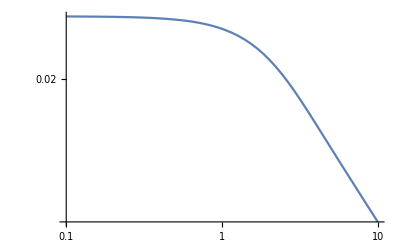

```mathematica
LogLogPlot[SmearedFunc[x],{x,.1,10}]
```

```mathematica
data=Table[{10^x,SmearedFunc[10^x]},{x,-1,1,.01}];
```

```mathematica
Export["./Smeared2PTExact.csv",data,"CSV"];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./Smeared2PTExact.csv"]]]
```